```mathematica
ClearAll["Global`*"]
```

```mathematica
f[a_,b_]:=4 Pi (-1+3 a r-2 a^2 r^3)/r Exp[-(a+b) r^2] r^2
```

```mathematica
H=ParallelTable[NIntegrate[f[a,b],{r,0,Infinity}],{a,{13,1.96,0.44,0.12}},{b,{13,1.96,0.44,0.12}}]
```

{{0.577368,0.0717194,-0.323206,-0.437105},{0.0717194,0.506469,-1.00354,-2.39107},{-0.323206,-1.00354,-2.68809,-7.46151},{-0.437105,-2.39107,-7.46151,-17.6552}}

```mathematica
S=ParallelTable[4Pi NIntegrate[Exp[-(a+b) r^2] r^2,{r,0,Infinity}],{a,{13,1.96,0.44,0.12}},{b,{13,1.96,0.44,0.12}}]
```

{{0.0420015,0.0962338,0.113012,0.117172},{0.0962338,0.717457,1.49764,1.85622},{0.113012,1.49764,6.74529,13.2875},{0.117172,1.85622,13.2875,47.3596}}

```mathematica
evals=Eigenvalues[{H,S}]
```

{21.1066,2.56989,-0.499276,0.106674}

```mathematica
evecs=Eigenvectors[{H,S}]
```

{{0.979887,-0.196342,0.0353385,-0.00478181},{0.00529653,-0.940548,0.335629,-0.0519034},{-0.348083,-0.593496,-0.677257,-0.260622},{-0.214747,-0.152054,-0.890996,0.369985}}

```mathematica
renormalize[evec_]:=If[Length[Select[evec,#<0&]]>=3,-evec,evec](*如果有3个坐标是负数就反向该向量*)
```

```mathematica
evecs=renormalize/@evecs
```

{{0.979887,-0.196342,0.0353385,-0.00478181},{0.00529653,-0.940548,0.335629,-0.0519034},{0.348083,0.593496,0.677257,0.260622},{0.214747,0.152054,0.890996,-0.369985}}

```mathematica
g=Table[evecs[[i]].{Exp[-13r^2],Exp[-1.96r^2],Exp[-0.44r^2],Exp[-0.12r^2]},{i,1,4}]
```

{0.979887 ⅇ^(-13 r^2)-0.196342 ⅇ^(-1.96 r^2)+0.0353385 ⅇ^(-0.44 r^2)-0.00478181 ⅇ^(-0.12 r^2),0.00529653 ⅇ^(-13 r^2)-0.940548 ⅇ^(-1.96 r^2)+0.335629 ⅇ^(-0.44 r^2)-0.0519034 ⅇ^(-0.12 r^2),0.348083 ⅇ^(-13 r^2)+0.593496 ⅇ^(-1.96 r^2)+0.677257 ⅇ^(-0.44 r^2)+0.260622 ⅇ^(-0.12 r^2),0.214747 ⅇ^(-13 r^2)+0.152054 ⅇ^(-1.96 r^2)+0.890996 ⅇ^(-0.44 r^2)-0.369985 ⅇ^(-0.12 r^2)}

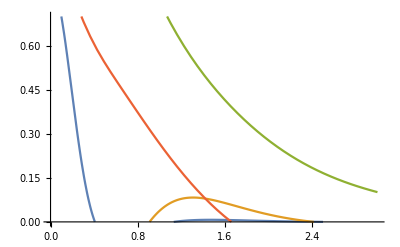

```mathematica
Plot[g,{r,0,3},PlotRange->{0,0.7}]
```